```mathematica
Clear["Global`*"];
```

```mathematica
Nk = 2000;Nac = 40;
beta = 0.7;
lambda = 0.8; (*um*)
deltak = 2*π/(beta*lambda);
dk = deltak/Nac;
krange=dk*Table[x,{x,-Nk/2,Nk/2,1}];
sigmak = 0.1*deltak;
```

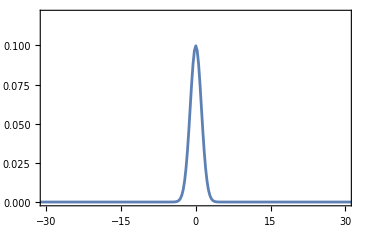

```mathematica
psik0 =Sqrt[dk]*Exp[-krange^2/(4*sigmak^2)]/Sqrt[sigmak *Sqrt[2*Pi]];
ListPlot[Transpose[{krange,Abs[psik0]^2}],Joined->True,Frame->True,PlotRange->{{-30,30},{0,0.12}}]
```

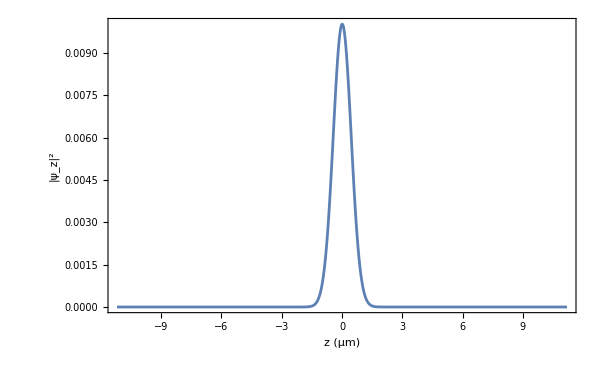

```mathematica
dz = 2*Pi/(dk*Nk);
zrange=dz*Table[x,{x,-Nk/2,Nk/2,1}];
psiz0 = RotateLeft[Fourier[psik0],Nk/2];
ListPlot[Transpose[{zrange,Abs[psiz0]^2}],Joined->True,PlotRange->All,ImageSize->600,FrameLabel->{Style["z (μm)",32],Style["|ψ_z|^2",32]},LabelStyle->{27,FontFamily->"Times New Roman"},Frame->True]
```

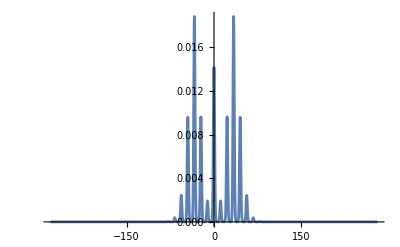

```mathematica
gL=4.2;
xi = 0.0015;
psizm = Exp[I*gL*Sin[zrange*deltak]]*psiz0;
psikm= RotateLeft[InverseFourier[psizm],0]*Exp[-I*xi*krange^2];
ListPlot[Transpose[{krange,Abs[psikm]^2}],Joined->True,PlotRange->All]
```

```mathematica
psizf= RotateLeft[Fourier[psikm],0*Nk/2];
Db =  Exp[I*zrange*deltak];
b=Dot[Conjugate[psizf],Db*psizf]
b2=Dot[Conjugate[psizf],Db^2*psizf]
```

7.88661×10^-7+0.567246 ⅈ

-0.484815-9.383×10^-8 ⅈ

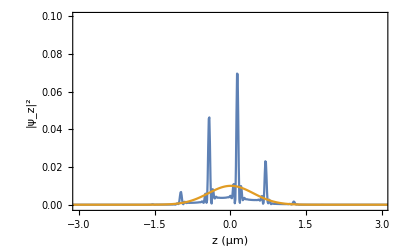

```mathematica
ListPlot[{Transpose[{zrange,Abs[psizf]^2}],Transpose[{zrange,Abs[psiz0]^2}]},Joined->True,PlotRange->{{-3,3},{-0.001,0.1}},ImageSize->600,FrameLabel->{Style["z (μm)",32],Style["|ψ_z|^2",32]},LabelStyle->{27,FontFamily->"Times New Roman"},Frame->True]
```

```mathematica
Dot[Conjugate[psizf],psizf]
```

1.+4.24362×10^-52 ⅈ

## symbolic operation for pure state

```mathematica
S={{Cos[g],-I Sin[g] Exp[-I ϕg]Conjugate[b]},{-I Sin[g] Exp[I ϕg]b,Cos[g]}};
```

```mathematica
(*S//MatrixForm*)
```

(Cos[g] | -ⅈ ⅇ^(-ⅈ ϕg) Conjugate[b] Sin[g]
-ⅈ b ⅇ^(ⅈ ϕg) Sin[g] | Cos[g])

```mathematica
ψ={Sin[θ/2],Exp[I ϕ]Cos[θ/2]};
(*ψ=ψ//MatrixForm*)
```

```mathematica
ψf=Dot[S,ψ]
(*ψf=ψf//MatrixForm*)
```

{-ⅈ ⅇ^(ⅈ ϕ-ⅈ ϕg) Conjugate[b] Cos[θ/2] Sin[g]+Cos[g] Sin[θ/2],ⅇ^(ⅈ ϕ) Cos[g] Cos[θ/2]-ⅈ b ⅇ^(ⅈ ϕg) Sin[g] Sin[θ/2]}

```mathematica
ψfdag={I  ⅇ^(-I ϕ+I ϕg) b Cos[θ/2] Sin[g]+Cos[g] Sin[θ/2],ⅇ^(-I ϕ) Cos[g] Cos[θ/2]+I ⅇ^(-I ϕg) Sin[g] Sin[θ/2] Conjugate[b]};
(*ψfdag=ψfdag//MatrixForm*)
```

```mathematica
rhof=KroneckerProduct[ψfdag,ψf]
```

{{(ⅈ b ⅇ^(-ⅈ ϕ+ⅈ ϕg) Cos[θ/2] Sin[g]+Cos[g] Sin[θ/2]) (-ⅈ ⅇ^(ⅈ ϕ-ⅈ ϕg) Conjugate[b] Cos[θ/2] Sin[g]+Cos[g] Sin[θ/2]),(ⅈ b ⅇ^(-ⅈ ϕ+ⅈ ϕg) Cos[θ/2] Sin[g]+Cos[g] Sin[θ/2]) (ⅇ^(ⅈ ϕ) Cos[g] Cos[θ/2]-ⅈ b ⅇ^(ⅈ ϕg) Sin[g] Sin[θ/2])},{(-ⅈ ⅇ^(ⅈ ϕ-ⅈ ϕg) Conjugate[b] Cos[θ/2] Sin[g]+Cos[g] Sin[θ/2]) (ⅇ^(-ⅈ ϕ) Cos[g] Cos[θ/2]+ⅈ ⅇ^(-ⅈ ϕg) Conjugate[b] Sin[g] Sin[θ/2]),(ⅇ^(ⅈ ϕ) Cos[g] Cos[θ/2]-ⅈ b ⅇ^(ⅈ ϕg) Sin[g] Sin[θ/2]) (ⅇ^(-ⅈ ϕ) Cos[g] Cos[θ/2]+ⅈ ⅇ^(-ⅈ ϕg) Conjugate[b] Sin[g] Sin[θ/2])}}

```mathematica
rhof[[1,1]]//Expand
```

b Conjugate[b] Cos[θ/2]^2 Sin[g]^2+ⅈ b ⅇ^(-ⅈ ϕ+ⅈ ϕg) Cos[g] Cos[θ/2] Sin[g] Sin[θ/2]-ⅈ ⅇ^(ⅈ ϕ-ⅈ ϕg) Conjugate[b] Cos[g] Cos[θ/2] Sin[g] Sin[θ/2]+Cos[g]^2 Sin[θ/2]^2

```mathematica
rhof[[2,1]]//Expand
```

-ⅈ ⅇ^(-ⅈ ϕg) Conjugate[b] Cos[g] Cos[θ/2]^2 Sin[g]+ⅇ^(-ⅈ ϕ) Cos[g]^2 Cos[θ/2] Sin[θ/2]+ⅇ^(ⅈ ϕ-2 ⅈ ϕg) Conjugate[b]^2 Cos[θ/2] Sin[g]^2 Sin[θ/2]+ⅈ ⅇ^(-ⅈ ϕg) Conjugate[b] Cos[g] Sin[g] Sin[θ/2]^2

```mathematica
rhof[[1,2]]//Expand
```

ⅈ b ⅇ^(ⅈ ϕg) Cos[g] Cos[θ/2]^2 Sin[g]+ⅇ^(ⅈ ϕ) Cos[g]^2 Cos[θ/2] Sin[θ/2]+b^2 ⅇ^(-ⅈ ϕ+2 ⅈ ϕg) Cos[θ/2] Sin[g]^2 Sin[θ/2]-ⅈ b ⅇ^(ⅈ ϕg) Cos[g] Sin[g] Sin[θ/2]^2

```mathematica
rhof[[2,2]]//Expand
```

Cos[g]^2 Cos[θ/2]^2-ⅈ b ⅇ^(-ⅈ ϕ+ⅈ ϕg) Cos[g] Cos[θ/2] Sin[g] Sin[θ/2]+ⅈ ⅇ^(ⅈ ϕ-ⅈ ϕg) Conjugate[b] Cos[g] Cos[θ/2] Sin[g] Sin[θ/2]+b Conjugate[b] Sin[g]^2 Sin[θ/2]^2

```mathematica
rho11=b Conjugate[b] Cos[θ/2]^2 Sin[g]^2+ⅈ b ⅇ^(-ⅈ ϕ+ⅈ ϕg) Cos[g] Cos[θ/2] Sin[g] Sin[θ/2]-ⅈ ⅇ^(ⅈ ϕ-ⅈ ϕg) Conjugate[b] Cos[g] Cos[θ/2] Sin[g] Sin[θ/2]+Cos[g]^2 Sin[θ/2]^2
```

b Conjugate[b] Cos[θ/2]^2 Sin[g]^2+ⅈ b ⅇ^(-ⅈ ϕ+ⅈ ϕg) Cos[g] Cos[θ/2] Sin[g] Sin[θ/2]-ⅈ ⅇ^(ⅈ ϕ-ⅈ ϕg) Conjugate[b] Cos[g] Cos[θ/2] Sin[g] Sin[θ/2]+Cos[g]^2 Sin[θ/2]^2

```mathematica
rho12=ⅈ b ⅇ^(ⅈ ϕg) Cos[g] Cos[θ/2]^2 Sin[g]+ⅇ^(ⅈ ϕ) Cos[g]^2 Cos[θ/2] Sin[θ/2]+b2 ⅇ^(-ⅈ ϕ+2 ⅈ ϕg) Cos[θ/2] Sin[g]^2 Sin[θ/2]-ⅈ b ⅇ^(ⅈ ϕg) Cos[g] Sin[g] Sin[θ/2]^2
```

ⅈ b ⅇ^(ⅈ ϕg) Cos[g] Cos[θ/2]^2 Sin[g]+ⅇ^(ⅈ ϕ) Cos[g]^2 Cos[θ/2] Sin[θ/2]+b2 ⅇ^(-ⅈ ϕ+2 ⅈ ϕg) Cos[θ/2] Sin[g]^2 Sin[θ/2]-ⅈ b ⅇ^(ⅈ ϕg) Cos[g] Sin[g] Sin[θ/2]^2

```mathematica
rho21=-ⅈ ⅇ^(-ⅈ ϕg) Conjugate[b] Cos[g] Cos[θ/2]^2 Sin[g]+ⅇ^(-ⅈ ϕ) Cos[g]^2 Cos[θ/2] Sin[θ/2]+ⅇ^(ⅈ ϕ-2 ⅈ ϕg) Conjugate[b2] Cos[θ/2] Sin[g]^2 Sin[θ/2]+ⅈ ⅇ^(-ⅈ ϕg) Conjugate[b] Cos[g] Sin[g] Sin[θ/2]^2
```

-ⅈ ⅇ^(-ⅈ ϕg) Conjugate[b] Cos[g] Cos[θ/2]^2 Sin[g]+ⅇ^(-ⅈ ϕ) Cos[g]^2 Cos[θ/2] Sin[θ/2]+ⅇ^(ⅈ ϕ-2 ⅈ ϕg) Conjugate[b2] Cos[θ/2] Sin[g]^2 Sin[θ/2]+ⅈ ⅇ^(-ⅈ ϕg) Conjugate[b] Cos[g] Sin[g] Sin[θ/2]^2

```mathematica
rho22=Cos[g]^2 Cos[θ/2]^2-ⅈ b ⅇ^(-ⅈ ϕ+ⅈ ϕg) Cos[g] Cos[θ/2] Sin[g] Sin[θ/2]+ⅈ ⅇ^(ⅈ ϕ-ⅈ ϕg) Conjugate[b] Cos[g] Cos[θ/2] Sin[g] Sin[θ/2]+b Conjugate[b] Sin[g]^2 Sin[θ/2]^2
```

Cos[g]^2 Cos[θ/2]^2-ⅈ b ⅇ^(-ⅈ ϕ+ⅈ ϕg) Cos[g] Cos[θ/2] Sin[g] Sin[θ/2]+ⅈ ⅇ^(ⅈ ϕ-ⅈ ϕg) Conjugate[b] Cos[g] Cos[θ/2] Sin[g] Sin[θ/2]+b Conjugate[b] Sin[g]^2 Sin[θ/2]^2

```mathematica
θ=π/4;ϕ=π/3;ϕg=0;g=0.1;
```

```mathematica
z=rho22-rho11
```

0.737635+0. ⅈ

```mathematica
x=rho12+Conjugate[rho12]
```

0.269209+0. ⅈ

```mathematica
y=(rho12-Conjugate[rho12])/I
```

0.608233+0. ⅈ

```mathematica
x^2+y^2+z^2
```

0.986526+0. ⅈ

## symbolic operation for mixed state

```mathematica
S={{Cos[g],-I Sin[g] Exp[-I ϕg]Conjugate[b]},{-I Sin[g] Exp[I ϕg]b,Cos[g]}};
Sdag={{Cos[g],I Sin[g] Exp[I ϕg]b},{I Sin[g] Exp[-I ϕg]Conjugate[b],Cos[g]}};
r11=rho11;
r22=rho22;
r12=rho12;
r21=rho21;
```

```mathematica
RhoMix={{r11,r12},{r21,r22}};
```

```mathematica
RhoMixf=Dot[S,Dot[RhoMix,Sdag]];
```

```mathematica
RhoMixf[[1,1]]
```

```mathematica
RhoMixf[[1,2]]
```

```mathematica
RhoMixf[[2,1]]
```

```mathematica
RhoMixf[[2,2]]
```

```mathematica
Mrho[rhoin_,g_,ϕg_,b1_,b2_]:=Module[{r11,r12,r21,r22,rf11,rf12,rf22,rhof},

r11=rhoin[[1,1]];r12=rhoin[[1,2]];r21=rhoin[[2,1]];r22=rhoin[[2,2]];

rf11=Cos[g] (r11 Cos[g]+r12 b1 I Exp[I ϕg]Sin[g])-Conjugate[b1]I Exp[- I ϕg] Sin[g] ( r21 Cos[g]+r22 b1 I Exp[I ϕg] Sin[g]);

rf12=Cos[g] (r12 Cos[g]+r11 Conjugate[b1]I Exp[-I ϕg] Sin[g])-I Exp[-I ϕg] Sin[g] ( r22 Conjugate[b1]Cos[g]+r21 Conjugate[b2] I Exp[-I ϕg] Sin[g]);

rf22=Cos[g] (r22 Cos[g]+r21 Conjugate[b1]I  Exp[-I ϕg] Sin[g])-b1 I Exp[I ϕg] Sin[g] (r12 Cos[g]+r11 Conjugate[b1]I Exp[-I ϕg] Sin[g]);

rhof={{rf11,rf12},{Conjugate[rf12],rf22}}]
```

```mathematica
beta = 0.7;
lambda = 0.8; (*um*)
deltak = 2*π/(beta*lambda);
sigmak = 0.1*deltak;
xi = 0.0015;gL=4.2;
factorbunch[gL_,L_,n_]:=Module[{Nk,Nac,dk,krange,dz,zrange,psik0,psiz0,psizm,psikm,psizf,psizfn,Db,bn},
Nk = 2000;Nac = 40;dk = deltak/Nac;
krange=dk*Table[x,{x,-Nk/2,Nk/2,1}];
dz = 2*Pi/(dk*Nk);
zrange=dz*Table[x,{x,-Nk/2,Nk/2,1}];
psik0 =Sqrt[dk]*Exp[-krange^2/(4*sigmak^2)]/Sqrt[sigmak *Sqrt[2*Pi]];
psiz0 = RotateLeft[Fourier[psik0],Nk/2];
psizm = Exp[I*gL*Sin[zrange*deltak]]*psiz0;
psikm= RotateLeft[InverseFourier[psizm],0]*Exp[-I*L*krange^2];
psizf= RotateLeft[Fourier[psikm],0*Nk/2];
Db =  Exp[I*zrange*deltak];
bn=Dot[Conjugate[psizf],(Db^n)*psizf]
]
```

```mathematica
b1=factorbunch[gL,xi,1]
b2=factorbunch[gL,xi,2]
```

```mathematica
ψ={Sin[θ/2],Exp[I ϕ]Cos[θ/2]};

rhoin=KroneckerProduct[Conjugate[ψ],ψ]
```

```mathematica
g=0.1;ϕg=0;
rhof=Mrho[rhoin,g,ϕg,b1,b2]
```

{{0.127803+0. ⅈ,0.134317+0.304614 ⅈ},{0.134317-0.304614 ⅈ,0.865438+0. ⅈ}}

```mathematica
z=rhof[[2,2]]-rhof[[1,1]]
x=rhof[[1,2]]+rhof[[2,1]]
y=(rhof[[1,2]]-rhof[[2,1]])/I
```

0.737635+0. ⅈ

0.268634+0. ⅈ

0.609228+0. ⅈ

```mathematica
x^2+y^2+z^2
```

0.987429+0. ⅈ